## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
```

## Geodesic equations

```mathematica
GeodRules={
P->𝔈(r^2+a^2)-a 𝔏,
B->𝔏-a 𝔈 Sin[θ]^2,
ℜ->P^2-Δ[r](r^2+𝔎),
𝒪->𝔎-a^2 Cos[θ]^2-B^2/Sin[θ]^2
};
```

```mathematica
GeodEqs={
t'[τ]==1/Σ[r,θ](a B+(r^2+a^2)/Δ[r] P),
ϕ'[τ]==1/Σ[r,θ](B/Sin[θ]^2+a/Δ[r] P),
r'[τ]==(Subscript[ϵ, R] Sqrt[ℜ])/Σ[r,θ],
θ'[τ]==(Subscript[ϵ, Θ] Sqrt[𝒪])/Σ[r,θ]
}//Map@Apply[#1==(#2//.GeodRules/.{r->r[τ],θ->θ[τ]})&];
```

```mathematica
solEL=ℜ==0&&Inactiveℜτ==0//.GeodRules/.{r->r[τ],θ->θ[τ]}//Activate//Expand//Solve[#/.r[τ]->r0,{𝔈,𝔏},Reals]&//FullSimplify[#,r0>0&&Δ[r0]>0&&𝔎>0]&
```

```mathematica
GyroEqs=GeodEqs⟦{1,2,4}⟧//.(Last@solEL∪{r[τ]->r0,𝔏->0}∪Simplify[First@Solve[0==𝔏/.Last@solEL,𝔎,Reals],a>0&&r0>0&&M>0&&M>(r0 (a^2+r0^2))/(-a^2+3 r0^2)&&a>√3 r0])/.{a->𝒥,M->1}//
Simplify[#,Reals]/.{Abs[x_]^2->x^2}&;
```

```mathematica
solN=First@NDSolve[Join[GyroEqs,{t[0]==0,θ[0]==0,ϕ[0]==0}]/.{𝒥->0.7,r0->10,Subscript[ϵ, R]->1,Subscript[ϵ, Θ]->1},{t,θ,ϕ},{τ,0,12000}]
ParametricPlot3D[{Sin[θ[τ]]Cos[ϕ[τ]],Sin[θ[τ]]Sin[ϕ[τ]],Cos[θ[τ]]}/.solN//Evaluate,{τ,0,12000},ColorFunction->(ColorData["SolarColors"][t[#4]/.solN//Evaluate]&)]
```

{t→InterpolatingFunction[…],θ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}

-Graphics3D-

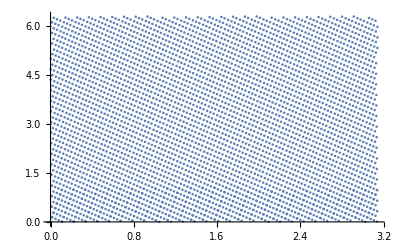

```mathematica
Table[{Mod[θ[τ],Pi],Mod[ϕ[τ],2Pi]}/.solN,{τ,0,12000,3}]//ListPlot
```